# “Popularity versus similarity in growing networks”

### Parametry symulacji

```mathematica
ClearAll["Global `*"];  (* czyszczenie jądra programu ze wszystkich zmiennych *)
nmax=10;
m=2;
```

### Interfejs graficzny

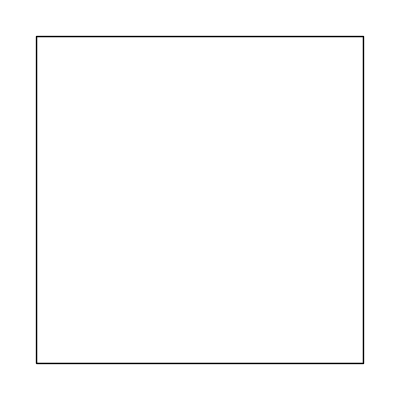

```mathematica
ramka=Graphics[Line[{{-nmax,-nmax},{nmax,-nmax},{nmax,nmax},{-nmax,nmax},{-nmax,-nmax}}]];
Show[ramka]
```

```mathematica
punkty={};
wp[n_]:=(
phi=2 Π RandomReal[];
{n,phi}
)
```

```mathematica
wp[3]
```

(3
1.51493 Π)

```mathematica
wp[3][[1]]
```

3

```mathematica
wp[3][[2]]
```

1.70215 Π

```mathematica
p=Graphics[Point[{wp[3][[1]] Cos[wp[3][[2]]],wp[3][[1]] Sin[wp[3][[2]]]}],PointSize[3]];
```

```mathematica
p1=(
r=wp[3][[1]];
theta=wp[3][[2]];
Print[r,"     ", theta];
Graphics[Point[{r Cos[theta],r Sin[theta]}]]);
p1
```

3     0.557469 Π

-Graphics-

```mathematica
Show[ramka,p1]
```

-Graphics-

```mathematica
wp[3]
```

(3
1.69991 Π)

```mathematica
wp[3][[1]]
wp[3][[2]]
```

3

0.286766 Π

```mathematica
punkty=Append[punkty,p]
```

(-Graphics-)

```mathematica
Show[{ramka,punkty}]
```

-Graphics-

```mathematica
For[i=1,i≤ nmax,i++,(
wp[i];
p=Point[{wp[i][[1]] Cos[wp[i][[2]]],wp[i][[1]] Sin[wp[i][[2]]]}];
punkty=Append[punkty,p];
)];
Show[{ramka,Graphics[punkty]}]
```

-Graphics-